```mathematica
Clear[MethodOfDescent];
MethodOfDescent[list_]:=Module[{l=list},
Clear[Overlap,slope,edges,edgeset,Tree];
Overlap=Partition[l,2,1];
slope[{a_,b_}]:=b-a;
edges[{a_,b_}]:={a->(b-a),b->(b-a)};
edgeset={};
Tree={list};
While[
Length[Overlap]≠0,
{
edgeset=Union[edgeset,Flatten[Map[edges,Overlap]]],
Overlap=Map[slope,Overlap],
If[Length[Overlap]==1,RootVertex=Overlap,Continue],
Overlap=Partition[Overlap,2,1]
};
];
Return[{edgeset,l,RootVertex}];
]
```

```mathematica
(*Reallocate Memory to store the data*)
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"];
```

```mathematica
(*Set Working Directory*)
(*Windows should be:*)
(*"C:\\Users\\<Username>\\<Where_ever_the_data_is_probably_Downloads>"*)
SetDirectory["/home/adam/Desktop/Modeling/Data"];
```

```mathematica
(*Load the data*)
Datastuff= Import["ProblemC56Var.xlsx"];
```

```mathematica
Clear[f]
(*To turn years to Ints*)
f[{x_,y_,z_,a_}]:={x,y,IntegerPart[z],a}
```

```mathematica
Clear[ModifiedData]
ModifiedData=Map[f,Datastuff[[1]]];
```

```mathematica
Clear[AZData,TXData,NMData,CAData,Produced,Consumed]
(*Separate Data by state*)
AZData=Cases[ModifiedData,{_,"AZ",_,_}];
TXData=Cases[ModifiedData,{_,"TX",_,_}];
NMData=Cases[ModifiedData,{_,"NM",_,_}];
CAData=Cases[ModifiedData,{_,"CA",_,_}];
StateData={AZData,TXData,NMData,CAData};

(*Separate By Production and Consumption*)
Consumed=Drop[Map[First,Datastuff[[2]]],2];
Produced=Flatten@Drop[Drop[Map[Take[#,{4}]&,Datastuff[[2]]],2],-34];
```

```mathematica
Clear[TimeFunc,VarFunc,RemoveState,ProducedVars,ConsumedVars,DataFunc]
(*Functions for Working With Arrays*)
VarFunc[{a_,b_,c_,d_}]:={a}
TimeFunc[{a_,b_,c_,d_}]:={c,d}
RemoveState[{a_,b_,c_,d_}]:={a,c,d}
DataFunc[{a_,b_,c_,d_}]:=d
ProducedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Produced}]];
ConsumedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Consumed}]];
```

```mathematica
Clear[AZProduced,TXProduced,NMProduced,CAProduced]
(*Separates Production Variables by State*)
{AZProduced,TXProduced,NMProduced,CAProduced}=Map[ProducedVars,StateData];
```

```mathematica
Clear[AZConsumed,TXConsumed,NMConsumed,CAConsumed]
(*Separates Consumption Variables by State*)
{AZConsumed,TXConsumed,NMConsumed,CAConsumed}=Map[ConsumedVars,StateData];
```

```mathematica
Transpose[Map[TimeFunc,Map[Part[#,-8]&,{AZConsumed,TXConsumed,NMConsumed,CAConsumed}][[4]]]]
```

{{1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009},{270161.,248178.,329046.,360333.,331757.,418518.,375877.,473192.,397366.,544918.,521978.,533790.,472312.,553162.,645073.,578578.,422852.,338073.,576601.,559806.,591928.,503654.,702808.,811006.,696740.,594659.,668070.,524441.,515856.,742318.,673022.,658177.,642496.,822465.,636060.,854611.,824981.,767469.,838296.,765492.,742639.,615358.,684706.,775047.,769403.,818803.,897232.,706849.,677502.,712704.}}

```mathematica
GraphBuilder[data_]:=Map[TimeSeries[#[[2]],{#[[1]]}]&,data]
```

```mathematica
Map[TimeFunc,AZConsumed,{2}];
```

```mathematica
ProducedVars
```

ProducedVars

```mathematica
DeleteCases[MapIndexed[ListLinePlot[#1,PlotLabel->Evaluate[Part[Consumed,#2[[1]]]]]&,GraphBuilder[Map[Transpose,Map[TimeFunc,TXConsumed,{2}],{1}]]],_ListLinePlot][[35;;37]]
```

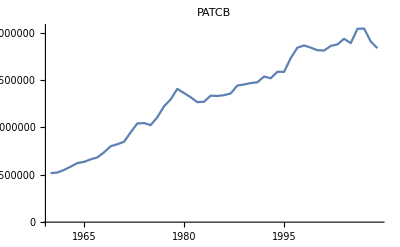
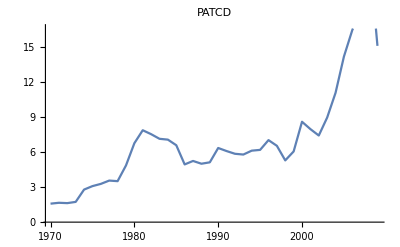
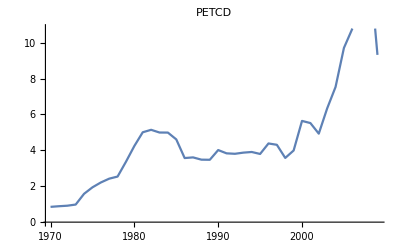
```mathematica
GraphicsRow[{-Graphics-,-Graphics-,-Graphics-}]
```

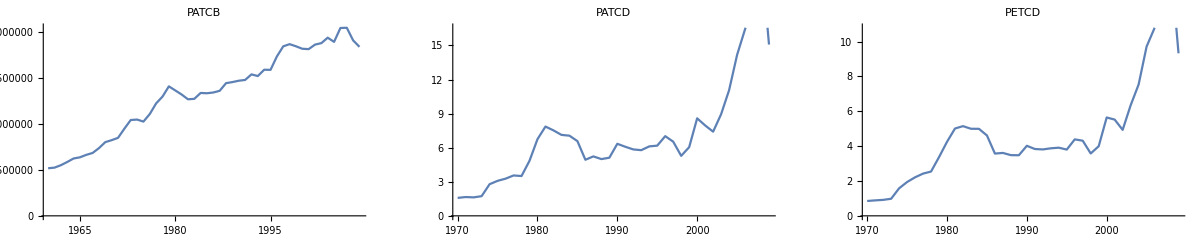

```mathematica
Export["/home/adam/Desktop/tx.pdf",%316,"PDF"]
```

/home/adam/Desktop/tx.pdf

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

ListLinePlot::lpn: TimeSeries[Transpose[{}]⟦2⟧,{{}}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

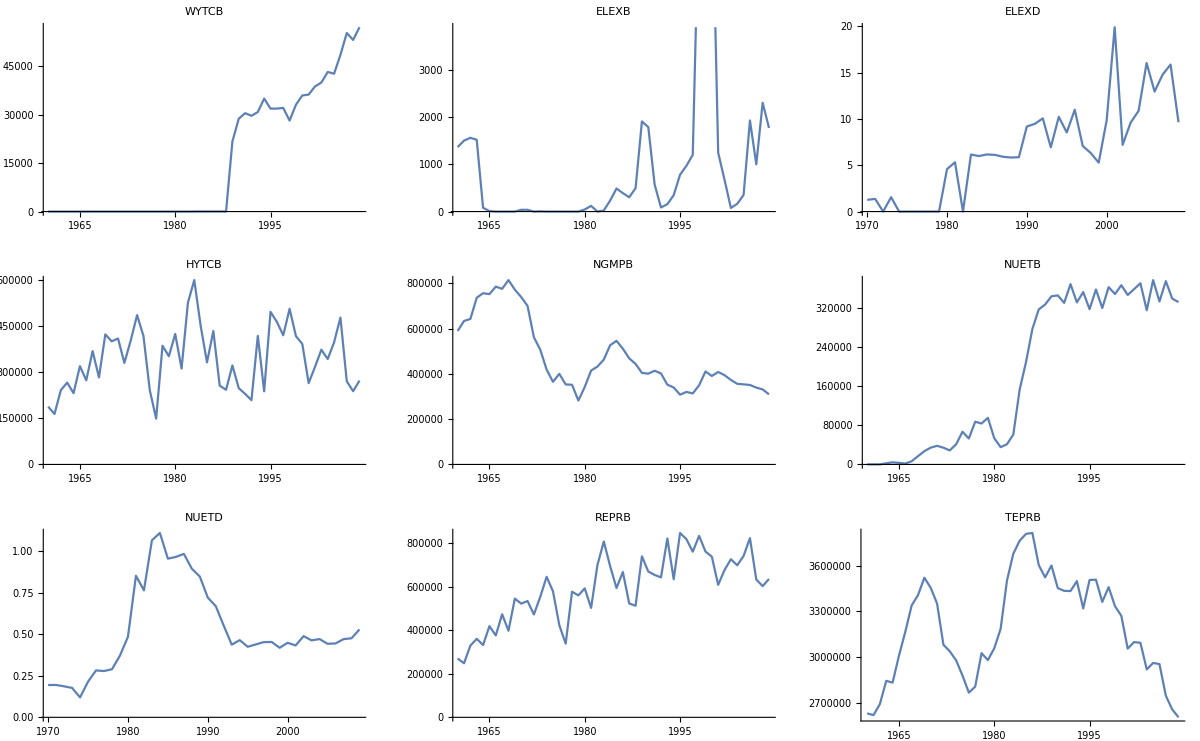

```mathematica
GraphicsGrid[Partition[DeleteCases[MapIndexed[ListLinePlot[#1,PlotLabel->Evaluate[Part[Produced,#2[[1]]]]]&,GraphBuilder[Map[Transpose,Map[TimeFunc,CAProduced,{2}],{1}]]],_ListLinePlot],3]]
```

```mathematica
Show[%258,ImageSize->Full]
```

-Graphics-

```mathematica
Export["/home/adam/Desktop/cavars.pdf",%259,"PDF"]
```

/home/adam/Desktop/cavars.pdf

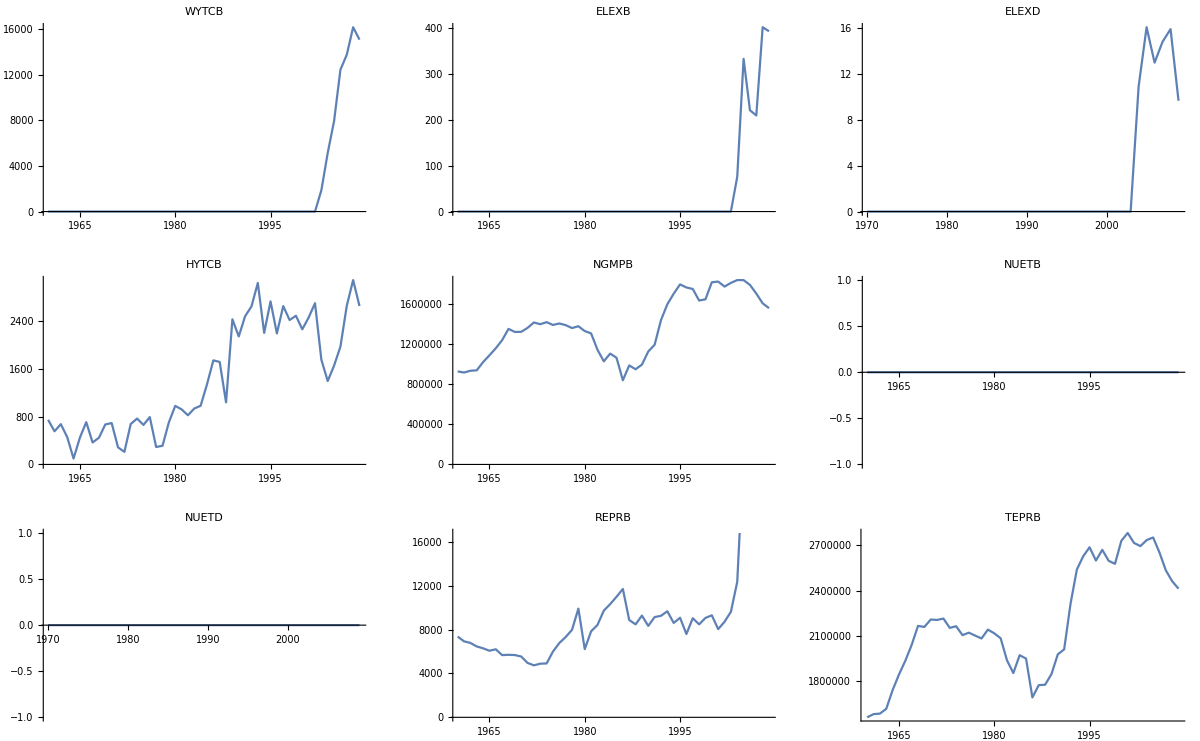

```mathematica
Show[%255,ImageSize->Full]
```

```mathematica
Export["/home/adam/Desktop/nmvars.pdf",%256,"PDF"]
```

/home/adam/Desktop/nmvars.pdf

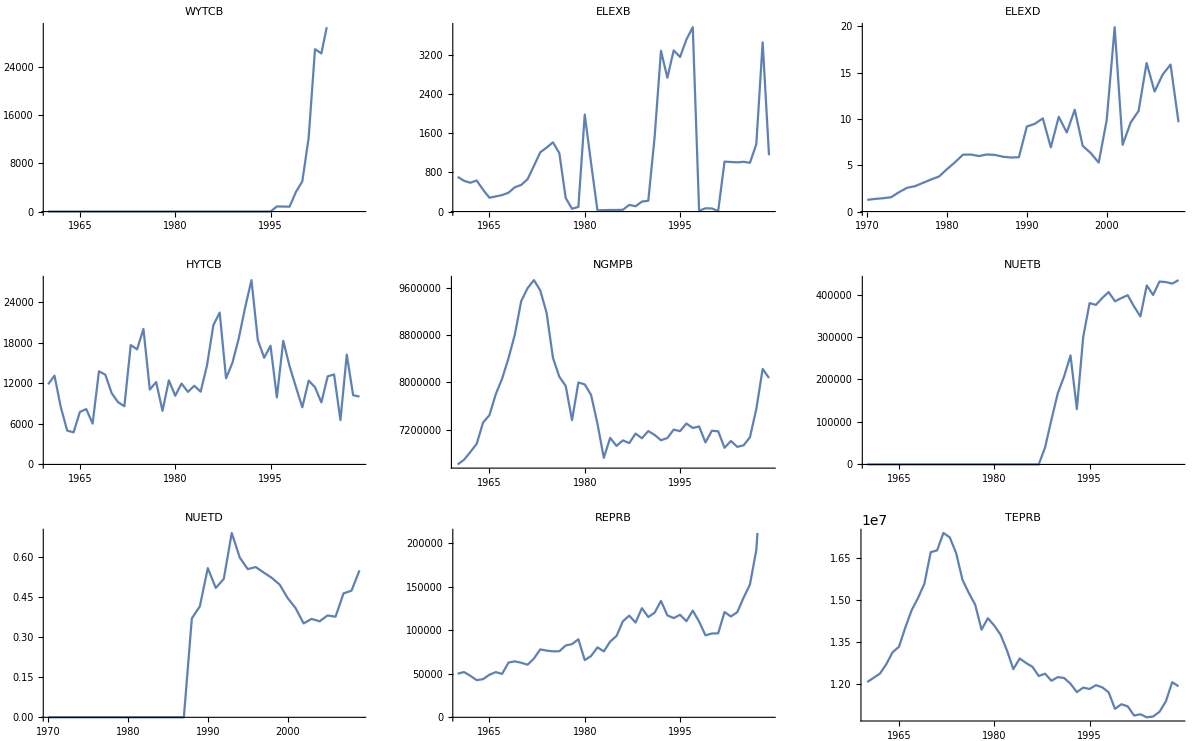

```mathematica
Show[%252,ImageSize->Full]
```

```mathematica
Export["/home/adam/Desktop/txvars.pdf",%253,"PDF"]
```

/home/adam/Desktop/txvars.pdf

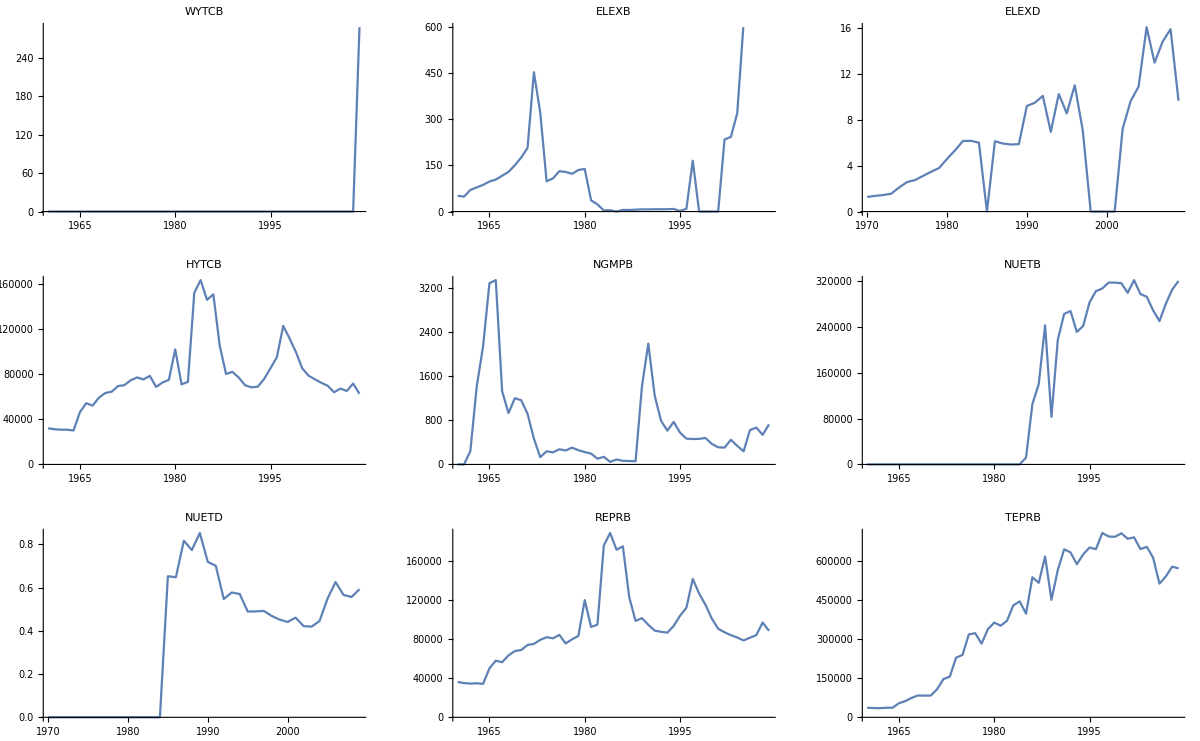

```mathematica
Show[%249,ImageSize->Full]
```

```mathematica
Export["/home/adam/Desktop/ArizonaVars.pdf",%250,"PDF"]
```

/home/adam/Desktop/ArizonaVars.pdf

```mathematica
CAProduced
```

{{{WYTCB,CA,1960,0.},{WYTCB,CA,1961,0.},{WYTCB,CA,1962,0.},{WYTCB,CA,1963,0.},{WYTCB,CA,1964,0.},{WYTCB,CA,1965,0.},{WYTCB,CA,1966,0.},{WYTCB,CA,1967,0.},{WYTCB,CA,1968,0.},{WYTCB,CA,1969,0.},{WYTCB,CA,1970,0.},{WYTCB,CA,1971,0.},{WYTCB,CA,1972,0.},{WYTCB,CA,1973,0.},{WYTCB,CA,1974,0.},{WYTCB,CA,1975,0.},{WYTCB,CA,1976,0.},{WYTCB,CA,1977,0.},{WYTCB,CA,1978,0.},{WYTCB,CA,1979,0.},{WYTCB,CA,1980,0.},{WYTCB,CA,1981,0.},{WYTCB,CA,1982,0.},{WYTCB,CA,1983,15.6981},{WYTCB,CA,1984,36.6785},{WYTCB,CA,1985,27.8341},{WYTCB,CA,1986,27.9415},{WYTCB,CA,1987,37.5226},{WYTCB,CA,1988,6.43165},{WYTCB,CA,1989,21684.9},{WYTCB,CA,1990,28697.9},{WYTCB,CA,1991,30415.8},{WYTCB,CA,1992,29619.5},{WYTCB,CA,1993,30758.3},{WYTCB,CA,1994,34941.6},{WYTCB,CA,1995,31830.6},{WYTCB,CA,1996,31836.1},{WYTCB,CA,1997,32036.9},{WYTCB,CA,1998,28122.},{WYTCB,CA,1999,33029.5},{WYTCB,CA,2000,35887.4},{WYTCB,CA,2001,36162.8},{WYTCB,CA,2002,38684.3},{WYTCB,CA,2003,39893.1},{WYTCB,CA,2004,43153.5},{WYTCB,CA,2005,42618.},{WYTCB,CA,2006,48432.5},{WYTCB,CA,2007,55201.5},{WYTCB,CA,2008,53063.3},{WYTCB,CA,2009,56996.6}},{},{},{{ELEXB,CA,1960,1363.42},{ELEXB,CA,1961,1500.85},{ELEXB,CA,1962,1560.03},{ELEXB,CA,1963,1518.82},{ELEXB,CA,1964,79.7453},{ELEXB,CA,1965,10.1132},{ELEXB,CA,1966,0.},{ELEXB,CA,1967,0.},{ELEXB,CA,1968,0.},{ELEXB,CA,1969,0.},{ELEXB,CA,1970,36.7152},{ELEXB,CA,1971,37.1729},{ELEXB,CA,1972,0.},{ELEXB,CA,1973,4.96374},{ELEXB,CA,1974,0.},{ELEXB,CA,1975,0.},{ELEXB,CA,1976,0.},{ELEXB,CA,1977,0.},{ELEXB,CA,1978,0.},{ELEXB,CA,1979,0.},{ELEXB,CA,1980,43.7418},{ELEXB,CA,1981,120.321},{ELEXB,CA,1982,0.},{ELEXB,CA,1983,23.4643},{ELEXB,CA,1984,233.009},{ELEXB,CA,1985,487.571},{ELEXB,CA,1986,389.862},{ELEXB,CA,1987,302.245},{ELEXB,CA,1988,495.143},{ELEXB,CA,1989,1906.38},{ELEXB,CA,1990,1787.18},{ELEXB,CA,1991,571.947},{ELEXB,CA,1992,86.3611},{ELEXB,CA,1993,156.515},{ELEXB,CA,1994,346.011},{ELEXB,CA,1995,779.587},{ELEXB,CA,1996,966.811},{ELEXB,CA,1997,1200.4},{ELEXB,CA,1998,6716.79},{ELEXB,CA,1999,4312.56},{ELEXB,CA,2000,7254.26},{ELEXB,CA,2001,1245.52},{ELEXB,CA,2002,671.901},{ELEXB,CA,2003,76.8041},{ELEXB,CA,2004,164.028},{ELEXB,CA,2005,351.61},{ELEXB,CA,2006,1926.73},{ELEXB,CA,2007,998.815},{ELEXB,CA,2008,2301.86},{ELEXB,CA,2009,1769.08}},{{ELEXD,CA,1970,1.2653},{ELEXD,CA,1971,1.36454},{ELEXD,CA,1972,0.},{ELEXD,CA,1973,1.55061},{ELEXD,CA,1974,0.},{ELEXD,CA,1975,0.},{ELEXD,CA,1976,0.},{ELEXD,CA,1977,0.},{ELEXD,CA,1978,0.},{ELEXD,CA,1979,0.},{ELEXD,CA,1980,4.5774},{ELEXD,CA,1981,5.32169},{ELEXD,CA,1982,0.},{ELEXD,CA,1983,6.15282},{ELEXD,CA,1984,5.99156},{ELEXD,CA,1985,6.16523},{ELEXD,CA,1986,6.11561},{ELEXD,CA,1987,5.91844},{ELEXD,CA,1988,5.83253},{ELEXD,CA,1989,5.86292},{ELEXD,CA,1990,9.18039},{ELEXD,CA,1991,9.46799},{ELEXD,CA,1992,10.0598},{ELEXD,CA,1993,6.93441},{ELEXD,CA,1994,10.2239},{ELEXD,CA,1995,8.54156},{ELEXD,CA,1996,10.9883},{ELEXD,CA,1997,7.08249},{ELEXD,CA,1998,6.31999},{ELEXD,CA,1999,5.28003},{ELEXD,CA,2000,9.85637},{ELEXD,CA,2001,19.8995},{ELEXD,CA,2002,7.19946},{ELEXD,CA,2003,9.60208},{ELEXD,CA,2004,10.8758},{ELEXD,CA,2005,16.0363},{ELEXD,CA,2006,12.9531},{ELEXD,CA,2007,14.7713},{ELEXD,CA,2008,15.8697},{ELEXD,CA,2009,9.635}},{{HYTCB,CA,1960,187705.},{HYTCB,CA,1961,163670.},{HYTCB,CA,1962,241087.},{HYTCB,CA,1963,265551.},{HYTCB,CA,1964,231188.},{HYTCB,CA,1965,319052.},{HYTCB,CA,1966,273247.},{HYTCB,CA,1967,368007.},{HYTCB,CA,1968,282561.},{HYTCB,CA,1969,422243.},{HYTCB,CA,1970,399628.},{HYTCB,CA,1971,408830.},{HYTCB,CA,1972,329587.},{HYTCB,CA,1973,402618.},{HYTCB,CA,1974,484740.},{HYTCB,CA,1975,417309.},{HYTCB,CA,1976,240578.},{HYTCB,CA,1977,148707.},{HYTCB,CA,1978,385489.},{HYTCB,CA,1979,351170.},{HYTCB,CA,1980,423618.},{HYTCB,CA,1981,311124.},{HYTCB,CA,1982,525065.},{HYTCB,CA,1983,598435.},{HYTCB,CA,1984,450580.},{HYTCB,CA,1985,331348.},{HYTCB,CA,1986,433077.},{HYTCB,CA,1987,255937.},{HYTCB,CA,1988,242347.},{HYTCB,CA,1989,321318.},{HYTCB,CA,1990,247490.},{HYTCB,CA,1991,229144.},{HYTCB,CA,1992,208571.},{HYTCB,CA,1993,417437.},{HYTCB,CA,1994,237398.},{HYTCB,CA,1995,495318.},{HYTCB,CA,1996,462729.},{HYTCB,CA,1997,419290.},{HYTCB,CA,1998,505243.},{HYTCB,CA,1999,416573.},{HYTCB,CA,2000,391043.},{HYTCB,CA,2001,263923.},{HYTCB,CA,2002,316794.},{HYTCB,CA,2003,372472.},{HYTCB,CA,2004,342160.},{HYTCB,CA,2005,396279.},{HYTCB,CA,2006,476582.},{HYTCB,CA,2007,270107.},{HYTCB,CA,2008,237755.},{HYTCB,CA,2009,272187.}},{{NGMPB,CA,1960,589695.},{NGMPB,CA,1961,633798.},{NGMPB,CA,1962,642889.},{NGMPB,CA,1963,736626.},{NGMPB,CA,1964,756640.},{NGMPB,CA,1965,752462.},{NGMPB,CA,1966,785759.},{NGMPB,CA,1967,776043.},{NGMPB,CA,1968,814571.},{NGMPB,CA,1969,772179.},{NGMPB,CA,1970,739624.},{NGMPB,CA,1971,700450.},{NGMPB,CA,1972,561778.},{NGMPB,CA,1973,507133.},{NGMPB,CA,1974,419144.},{NGMPB,CA,1975,365212.},{NGMPB,CA,1976,400199.},{NGMPB,CA,1977,353544.},{NGMPB,CA,1978,352084.},{NGMPB,CA,1979,282281.},{NGMPB,CA,1980,342208.},{NGMPB,CA,1981,414771.},{NGMPB,CA,1982,432487.},{NGMPB,CA,1983,463385.},{NGMPB,CA,1984,526963.},{NGMPB,CA,1985,546053.},{NGMPB,CA,1986,511411.},{NGMPB,CA,1987,468678.},{NGMPB,CA,1988,444233.},{NGMPB,CA,1989,404558.},{NGMPB,CA,1990,401147.},{NGMPB,CA,1991,414017.},{NGMPB,CA,1992,402192.},{NGMPB,CA,1993,352456.},{NGMPB,CA,1994,340053.},{NGMPB,CA,1995,308224.},{NGMPB,CA,1996,320466.},{NGMPB,CA,1997,313734.},{NGMPB,CA,1998,349864.},{NGMPB,CA,1999,410699.},{NGMPB,CA,2000,390975.},{NGMPB,CA,2001,408479.},{NGMPB,CA,2002,394507.},{NGMPB,CA,2003,373314.},{NGMPB,CA,2004,356232.},{NGMPB,CA,2005,353820.},{NGMPB,CA,2006,351100.},{NGMPB,CA,2007,339527.},{NGMPB,CA,2008,331493.},{NGMPB,CA,2009,309835.}},{{NUETB,CA,1960,0.51168},{NUETB,CA,1961,55.2726},{NUETB,CA,1962,83.8451},{NUETB,CA,1963,2287.61},{NUETB,CA,1964,4368.92},{NUETB,CA,1965,3192.78},{NUETB,CA,1966,1895.47},{NUETB,CA,1967,6502.68},{NUETB,CA,1968,17003.4},{NUETB,CA,1969,27127.1},{NUETB,CA,1970,34375.4},{NUETB,CA,1971,38137.5},{NUETB,CA,1972,34266.4},{NUETB,CA,1973,28689.3},{NUETB,CA,1974,41276.8},{NUETB,CA,1975,66855.4},{NUETB,CA,1976,53107.},{NUETB,CA,1977,87395.5},{NUETB,CA,1978,83800.6},{NUETB,CA,1979,95320.},{NUETB,CA,1980,53664.9},{NUETB,CA,1981,35367.1},{NUETB,CA,1982,41357.3},{NUETB,CA,1983,61214.2},{NUETB,CA,1984,153366.},{NUETB,CA,1985,209565.},{NUETB,CA,1986,277332.},{NUETB,CA,1987,317298.},{NUETB,CA,1988,327209.},{NUETB,CA,1989,344146.},{NUETB,CA,1990,345955.},{NUETB,CA,1991,330684.},{NUETB,CA,1992,369043.},{NUETB,CA,1993,331724.},{NUETB,CA,1994,352778.},{NUETB,CA,1995,317794.},{NUETB,CA,1996,358119.},{NUETB,CA,1997,320194.},{NUETB,CA,1998,362928.},{NUETB,CA,1999,348736.},{NUETB,CA,2000,366845.},{NUETB,CA,2001,346911.},{NUETB,CA,2002,358707.},{NUETB,CA,2003,370923.},{NUETB,CA,2004,315603.},{NUETB,CA,2005,377313.},{NUETB,CA,2006,333520.},{NUETB,CA,2007,375284.},{NUETB,CA,2008,339538.},{NUETB,CA,2009,332249.}},{{NUETD,CA,1970,0.19481},{NUETD,CA,1971,0.19499},{NUETD,CA,1972,0.18678},{NUETD,CA,1973,0.17737},{NUETD,CA,1974,0.12006},{NUETD,CA,1975,0.21481},{NUETD,CA,1976,0.28273},{NUETD,CA,1977,0.27902},{NUETD,CA,1978,0.28979},{NUETD,CA,1979,0.37256},{NUETD,CA,1980,0.48571},{NUETD,CA,1981,0.85316},{NUETD,CA,1982,0.76522},{NUETD,CA,1983,1.06709},{NUETD,CA,1984,1.11116},{NUETD,CA,1985,0.95629},{NUETD,CA,1986,0.9667},{NUETD,CA,1987,0.98528},{NUETD,CA,1988,0.89569},{NUETD,CA,1989,0.84845},{NUETD,CA,1990,0.72147},{NUETD,CA,1991,0.66993},{NUETD,CA,1992,0.55196},{NUETD,CA,1993,0.438},{NUETD,CA,1994,0.46513},{NUETD,CA,1995,0.42518},{NUETD,CA,1996,0.43932},{NUETD,CA,1997,0.45338},{NUETD,CA,1998,0.45416},{NUETD,CA,1999,0.41913},{NUETD,CA,2000,0.44942},{NUETD,CA,2001,0.43324},{NUETD,CA,2002,0.48926},{NUETD,CA,2003,0.46383},{NUETD,CA,2004,0.47161},{NUETD,CA,2005,0.44312},{NUETD,CA,2006,0.44535},{NUETD,CA,2007,0.47117},{NUETD,CA,2008,0.4765},{NUETD,CA,2009,0.5297}},{{REPRB,CA,1960,270161.},{REPRB,CA,1961,248178.},{REPRB,CA,1962,329046.},{REPRB,CA,1963,360333.},{REPRB,CA,1964,331757.},{REPRB,CA,1965,418518.},{REPRB,CA,1966,375877.},{REPRB,CA,1967,473192.},{REPRB,CA,1968,397366.},{REPRB,CA,1969,544918.},{REPRB,CA,1970,521978.},{REPRB,CA,1971,533790.},{REPRB,CA,1972,472312.},{REPRB,CA,1973,553162.},{REPRB,CA,1974,645073.},{REPRB,CA,1975,578578.},{REPRB,CA,1976,422852.},{REPRB,CA,1977,338073.},{REPRB,CA,1978,576601.},{REPRB,CA,1979,559806.},{REPRB,CA,1980,591928.},{REPRB,CA,1981,502232.},{REPRB,CA,1982,698981.},{REPRB,CA,1983,807128.},{REPRB,CA,1984,693614.},{REPRB,CA,1985,593488.},{REPRB,CA,1986,666981.},{REPRB,CA,1987,522673.},{REPRB,CA,1988,512100.},{REPRB,CA,1989,738965.},{REPRB,CA,1990,669385.},{REPRB,CA,1991,653581.},{REPRB,CA,1992,642313.},{REPRB,CA,1993,820857.},{REPRB,CA,1994,633675.},{REPRB,CA,1995,846265.},{REPRB,CA,1996,817766.},{REPRB,CA,1997,760363.},{REPRB,CA,1998,833064.},{REPRB,CA,1999,760982.},{REPRB,CA,2000,737523.},{REPRB,CA,2001,608143.},{REPRB,CA,2002,676325.},{REPRB,CA,2003,725742.},{REPRB,CA,2004,697820.},{REPRB,CA,2005,741051.},{REPRB,CA,2006,822410.},{REPRB,CA,2007,632368.},{REPRB,CA,2008,602233.},{REPRB,CA,2009,635062.}},{{TEPRB,CA,1960,2.6309×10^6},{TEPRB,CA,1961,2.61976×10^6},{TEPRB,CA,1962,2.69224×10^6},{TEPRB,CA,1963,2.84451×10^6},{TEPRB,CA,1964,2.83282×10^6},{TEPRB,CA,1965,3.00945×10^6},{TEPRB,CA,1966,3.16624×10^6},{TEPRB,CA,1967,3.33921×10^6},{TEPRB,CA,1968,3.40682×10^6},{TEPRB,CA,1969,3.52091×10^6},{TEPRB,CA,1970,3.45468×10^6},{TEPRB,CA,1971,3.35158×10^6},{TEPRB,CA,1972,3.08108×10^6},{TEPRB,CA,1973,3.03822×10^6},{TEPRB,CA,1974,2.97891×10^6},{TEPRB,CA,1975,2.8794×10^6},{TEPRB,CA,1976,2.76708×10^6},{TEPRB,CA,1977,2.80674×10^6},{TEPRB,CA,1978,3.02613×10^6},{TEPRB,CA,1979,2.98056×10^6},{TEPRB,CA,1980,3.05795×10^6},{TEPRB,CA,1981,3.18513×10^6},{TEPRB,CA,1982,3.50194×10^6},{TEPRB,CA,1983,3.67892×10^6},{TEPRB,CA,1984,3.76366×10^6},{TEPRB,CA,1985,3.80844×10^6},{TEPRB,CA,1986,3.81438×10^6},{TEPRB,CA,1987,3.60426×10^6},{TEPRB,CA,1988,3.52307×10^6},{TEPRB,CA,1989,3.60081×10^6},{TEPRB,CA,1990,3.45243×10^6},{TEPRB,CA,1991,3.43486×10^6},{TEPRB,CA,1992,3.43342×10^6},{TEPRB,CA,1993,3.49867×10^6},{TEPRB,CA,1994,3.31921×10^6},{TEPRB,CA,1995,3.50626×10^6},{TEPRB,CA,1996,3.50795×10^6},{TEPRB,CA,1997,3.36227×10^6},{TEPRB,CA,1998,3.45904×10^6},{TEPRB,CA,1999,3.33419×10^6},{TEPRB,CA,2000,3.27086×10^6},{TEPRB,CA,2001,3.05578×10^6},{TEPRB,CA,2002,3.09874×10^6},{TEPRB,CA,2003,3.09398×10^6},{TEPRB,CA,2004,2.91976×10^6},{TEPRB,CA,2005,2.9619×10^6},{TEPRB,CA,2006,2.95449×10^6},{TEPRB,CA,2007,2.74717×10^6},{TEPRB,CA,2008,2.65767×10^6},{TEPRB,CA,2009,2.60531×10^6}}}

```mathematica
timeseriesca=Union[GraphBuilder[Map[Transpose,Map[TimeFunc,CAProduced,{2}]]],GraphBuilder[Map[Transpose,Map[TimeFunc,CAProduced,{2}]]]]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[Transpose[{}]⟦2⟧,{{}}]}

```mathematica
timeseriesconsumed=Table[GraphBuilder[Map[Transpose,Map[TimeFunc,i,{2}]]],{i,{}}];
```

```mathematica
tsm=Map[TimeSeriesModelFit,timeseriesca];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

TimeSeriesModelFit::tsmfdt: The data TimeSeries[Transpose[{}]⟦2⟧,{{}}] cannot be interpreted as real-valued temporal data.

```mathematica
timeseriesconsumed=Table[GraphBuilder[Map[Transpose,Map[TimeFunc,i,{2}]]],{i,{AZProduced,TXProduced,NMProduced,CAProduced}}];
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 2 of Transpose[{}] does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
In[303]
```

Drop::drop: Cannot drop positions 1 through 29 in ….

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

GraphicsGrid::list: Drop[] is not a list of lists.

GraphicsGrid[Drop[]]

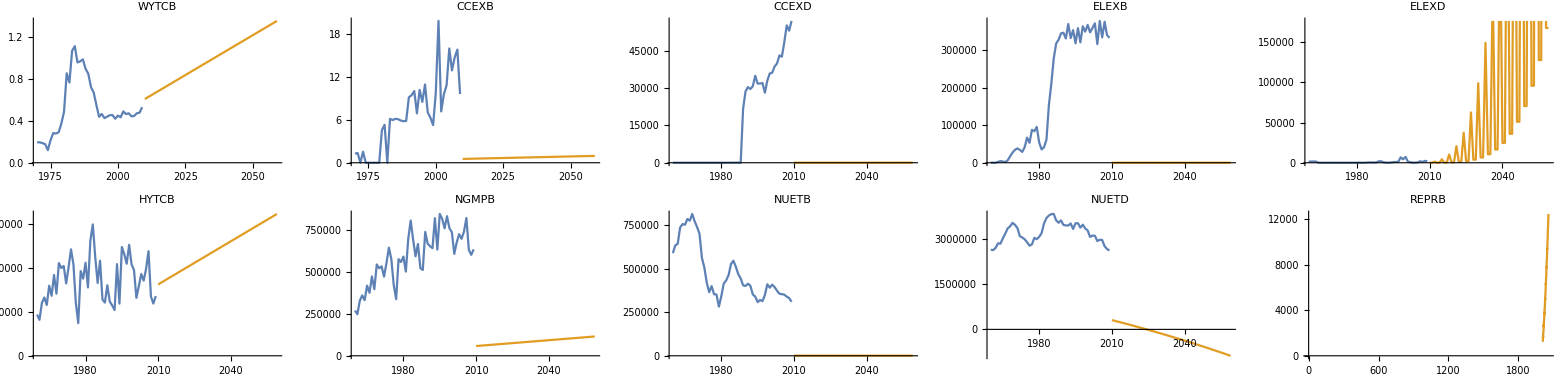

```mathematica
GraphicsGrid[Partition[Table[ListLinePlot[{timeseriesca[[i]],TimeSeriesForecast[tsm[[i]],{50}]},Ticks->None,PlotLabel->Produced[[i]]],{i,Length[timeseriesca]}],5]]
```

```mathematica
Show[%309,ImageSize->Full]
```

-Graphics-

```mathematica
Export["/home/adam/Desktop/energy_prod_ca.pdf",%310,"PDF"]
```

/home/adam/Desktop/energy_prod_ca.pdf

```mathematica
GraphicsGrid[Partition[Drop[Table[ListLinePlot[{timeseriesca[[i]],TimeSeriesForecast[tsm[[i]],{50}]},Ticks->None,PlotLabel->Produced[[i]]],{i,Length[timeseriesca]}],29],5]]
```

Drop::drop: Cannot drop positions 1 through 29 in ….

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

GraphicsGrid::list: Drop[] is not a list of lists.

GraphicsGrid[Drop[]]

```mathematica
Export["/home/adam/Desktop/pred.pdf",%290,"PDF"]
```

/home/adam/Desktop/pred.pdf

```mathematica
Show[%285,ImageSize->Large]
```

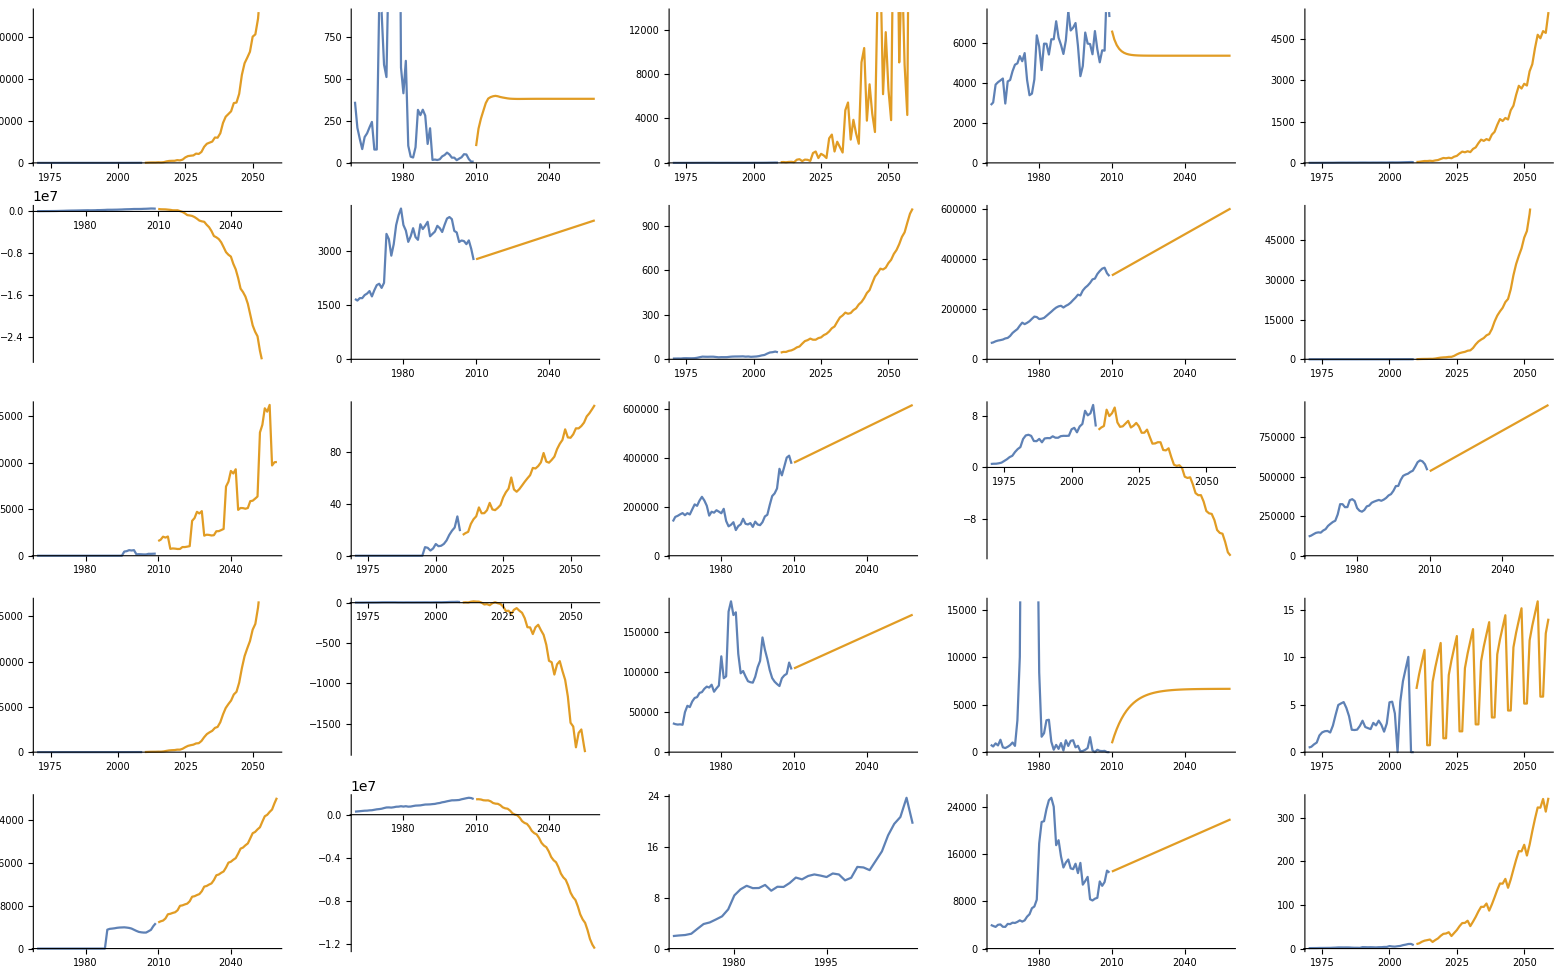

```mathematica
Show[%166,ImageSize->Full]
```

```mathematica
Export["/home/adam/Desktop/tsm.pdf",%276,"PDF",ImageSize->Full]
```

/home/adam/Desktop/tsm.pdf

```mathematica
Export["/home/adam/Desktop/pred.pdf",Show[%166,ImageSize->Full]]
```

/home/adam/Desktop/pred.pdf

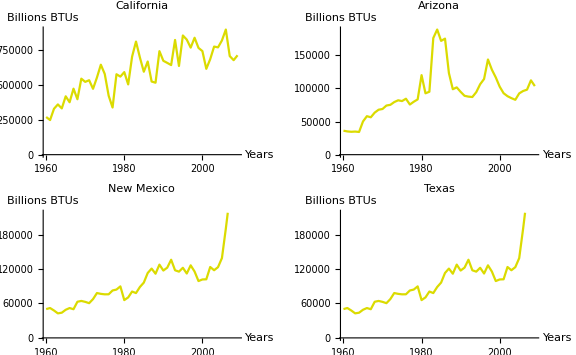

```mathematica
GraphicsGrid[{{e4,e1},{e3,e2}},ImageSize->Large]
```

```mathematica
Export["~/Desktop/TotalEnergy.pdf",%131]
```

~/Desktop/TotalEnergy.pdf

```mathematica
Clear[TimeRemove]
(*Define Datasets based on consumption and production of energy*)
TimeRemove[dataset_]:=Map[TimeFunc[#]&,dataset,{2}]
ProducedDat=Table[TimeRemove[i],{i,{AZProduced,TXProduced,NMProduced,CAProduced}}];
ConsumedDat=Table[TimeRemove[i],{i,{AZConsumed,TXConsumed,NMConsumed,CAConsumed}}];
```

```mathematica
(*Filter the Production Data*)
{AZPart,TXPart,NMPart,CAPart}=Table[
Map[
DataFunc,
i,
{2}],
{i,
{AZProduced,
TXProduced,
NMProduced,
CAProduced
}
}
];

(*Filter the Consumption Data*)
{AZPart0,TXPart0,NMPart0,CAPart0}=Table[
Map[
DataFunc,
i,
{2}],
{i,
{AZConsumed,
TXConsumed,
NMConsumed,
CAConsumed
}
}
];
```

```mathematica
(*Define Functions for calculation of slope using method of descent*)
Clear[RateOfChange,TableOfChange,OverlappedLists];
RateOfChange[{a_,b_}]:=b-a;
TableOfChange[data_]:=Table[RateOfChange[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];

Clear[ModelInitialization];
(*Initialize the model, this command must be run first using {AZPart,TXPart,NMPart,CAPart} or {AZPart0,TXPart0,NMPart0,CAPart0}*)
ModelInitialization[data_,OptionsForData_]:=Module[{d=data,o=OptionsForData},
{PSAZ,PSTX,PSNM,PSCA}=Map[OverlappedLists,d];
{PSAZ,PSTX,PSNM,PSCA}=Map[Table[TableOfChange[i],{i,#}]&,{PSAZ,PSTX,PSNM,PSCA}];
Slopes=Append[Slopes,Table[Map[o,i],{i,{PSAZ,PSTX,PSNM,PSCA}}]];
];
```

```mathematica
Clear[Model];
(*Modeling the data, m is the center of the Taylor Series, OptionForData can be Mean, Median, First, Last, etc...*)
Model[dataset_,m_,OptionForData_]:=Module[
{data0=dataset,o=OptionForData},

Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];

ModelInitialization[{PSAZ,PSTX,PSNM,PSCA},o];

n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];

Slopes={};
Slopes=Append[Slopes,Table[Map[o,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
ModelInitialization[{AZPart,TXPart,NMPart,CAPart},o];
While[
n<49,
{ModelInitialization[{PSAZ,PSTX,PSNM,PSCA},o]}
;n++];

CenterOfSeries=m;

Clear[TaylorSeries];
TaylorSeries[x_,{n0_}]:=x*(t-CenterOfSeries)^(n0-1)*(1/Factorial[n0]);

Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes];
{AZSlopes,
TXSlopes,
NMSlopes,
CASlopes}=
Table[
Transpose[
PadRight[
Map[
Part[#,1]&,
Table[
Map[
DeleteCases[#,_Last]&,
i],
{i,
Drop[
Slopes,
-1]
}
]
]
]
],
{j,
{1,
2,
3,
4}
}
];

{AZMonomials,
TXMonomials,
NMMonomials,
CAMonomials}=
Table[
Table[
MapIndexed[
TaylorSeries,
i],
{i,
j}
],
{j,
{AZSlopes,
TXSlopes,
NMSlopes,
CASlopes}
}
];

{AZSystemConsumption,
TXSystemConsumption,
NMSystemConsumption,
CASystemConsumption}=
Table[
Map[Total[#]&,
i],
{i,
{AZMonomials,
TXMonomials,
NMMonomials,
CAMonomials}
}
];

Return[
{AZSystemConsumption,
TXSystemConsumption,
NMSystemConsumption,
CASystemConsumption}
];
]
```

```mathematica
(*DO NOT REMOVE*)
ModelInitialization[{AZPart,TXPart,NMPart,CAPart},Last];
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Append::normal: Nonatomic expression expected at position 1 in Append[Slopes,{{288.359,Last[{}],Last[{}],11.6835,-6.23467,-9064.39,189.831,14967.5,0.03591,-8563.13,-6732.68},{«1»},«1»,{3933.23,«9»,-«18»}}].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[Slopes,{{288.359,Last[{}],Last[{}],11.6835,-6.23467,-9064.39,189.831,14967.5,0.03591,-8563.13,-6732.68},{«1»},«1»,{3933.23,«9»,-«18»}}].

```mathematica
Clear[s1]
s1=Model[{AZProduced,TXProduced,NMProduced,CAProduced},49,Last];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[Slopes,{{288.359,Last[{}],Last[{}],11.6835,-6.23467,-9064.39,189.831,14967.5,0.03591,-8563.13,-6732.68},{«1»},«1»,{3933.23,«9»,-«18»}}].

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

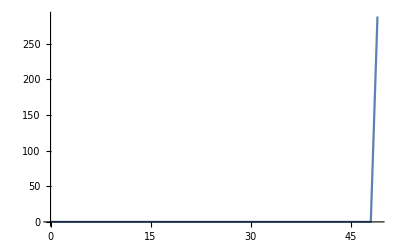

```mathematica
Show[ListLinePlot[TimeSeries[Transpose[ProducedDat[[1]][[1]]][[2]],{Transpose[ProducedDat[[1]][[1]]][[1]]}-1960]],Plot[s1[[1]][[1]],{t,0,55},PlotStyle->Orange]]
```

```mathematica
Clear[s2]
s2=Model[{AZConsumed,TXConsumed,NMConsumed,CAConsumed},49,Last];
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

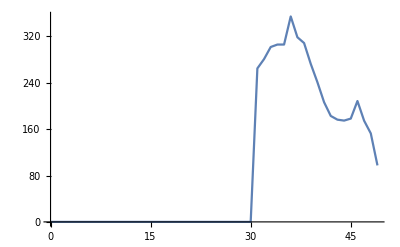

```mathematica
Show[ListLinePlot[TimeSeries[Transpose[ConsumedDat[[1]][[1]]][[2]],{Transpose[ConsumedDat[[1]][[1]]][[1]]}-1960]],Plot[s2[[1]][[1]],{t,0,55},PlotStyle->Orange]]
```

```mathematica
Clear[pathModel];
pathModel[dataset_,{indx1_,indx2_,indx3_}]:=MethodOfDescent[Transpose[dataset[[indx1]][[indx2]]][[indx3]]];
```

```mathematica
Clear[TaylorSeries0];
TaylorSeries0[x_,{n0_},m_]:=x*(t-m+1)^(n0-1)*(1/Factorial[n0]);
```

```mathematica
Clear[PathingTaylorSeries]
PathingTaylorSeries[dataset_,{indx1_,indx2_,indx3_},m_,VertexNum_]:=Show[
ListLinePlot[
TimeSeries[
Transpose[
dataset[[indx1]][[indx2]]][[indx3+1]],
{Transpose[dataset[[indx1]][[indx2]]][[indx3]]}-1960]
],
Plot[
Total[
MapIndexed[
TaylorSeries0[#1,{#2},m]&,
FindShortestPath[
graph1,
g1[[2]][[VertexNum]],
g1[[3]][[1]]
]
]
],
{t,0,55},
PlotStyle->Orange]
]
```

```mathematica
Clear[PathingTaylorSeriesLinkedbyVertexIndx]
PathingTaylorSeriesLinkedbyVertexIndx[dataset_,{indx1_,indx2_,indx3_}]:=Module[{},
g1=pathModel[dataset,{indx1,indx2,indx3+1}];
graph1=Graph[g1[[1]],GraphLayout->"LayeredDigraphEmbedding",ImageSize->Medium];
MinPaths=Table[
FindShortestPath[
graph1,
g1[[2]][[i]],
g1[[3]][[1]]
],{i,1,50}
];
ShortestPaths=Table[Total[
MapIndexed[
TaylorSeries0[#1,{#2},i-1]&,
MinPaths[[i]]
]
],
{i,1,50}];
Print["Making Plots, this might take awhile..."];
count=0;
Print[ProgressIndicator[Dynamic[count],{0,49}]];
Plots=Map[{Plot[
ShortestPaths[[#]],
{t,0,50},
PlotStyle->Orange],count++}&,Range[50]];
Deploy[
Manipulate[GraphicsRow[{
Show[
ListLinePlot[
TimeSeries[
Transpose[
dataset[[indx1]][[indx2]]][[indx3+1]],
{Transpose[dataset[[indx1]][[indx2]]][[indx3]]}-1960]
,ImageSize->Medium],
Plots[[VertexIndex]][[1]]
],HighlightGraph[graph1,PathGraph[MinPaths[[VertexIndex]],DirectedEdges->True]]}]
,{VertexIndex},{{VertexIndex,1,"Vertex Index"},1,50,1}
,FrameMargins->50]
]
]
```

```mathematica
PathingTaylorSeries[ConsumedDat,{1,1,1},43,44]
```

FindShortestPath::graph: A graph object is expected at position 1 in FindShortestPath[{1. graph1},{-20.9994 g1⟦2⟧⟦44⟧},{293.984 g1}].

FindShortestPath::graph: A graph object is expected at position 1 in FindShortestPath[{1. graph1},{-20.4382 g1⟦2⟧⟦44⟧},{278.48 g1}].

FindShortestPath::graph: A graph object is expected at position 1 in FindShortestPath[{1. graph1},{-19.877 g1⟦2⟧⟦44⟧},{263.396 g1}].

General::stop: Further output of FindShortestPath::graph will be suppressed during this calculation.

-Graphics-

```mathematica
paths=PathingTaylorSeriesLinkedbyVertexIndx[ConsumedDat,{1,1,1}]
```

Making Plots, this might take awhile...

HighlightGraph::graph: A graph object is expected at position 1 in HighlightGraph[{«1»},].

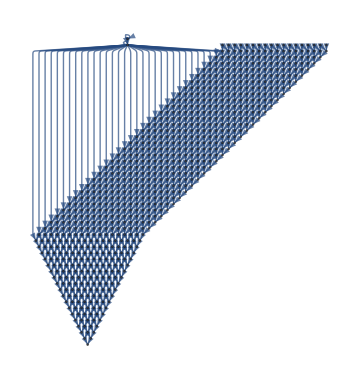

```mathematica
graph1
```

```mathematica
Export["~/Desktop/MethodOfDescent.pdf",Graph[%70,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name",ImageSize->Large]]
```

~/Desktop/MethodOfDescent.pdf

```mathematica
g1=MethodOfDescent[RandomReal[20,10]]
```

{{-229.047->-411.019,-70.0899->-229.047,-68.6691->-23.0153,-68.6691->158.957,-57.0416->-68.6691,-57.0416->90.2878,-46.9584->57.2813,-45.6538->-23.0153,-35.0912->-57.0416,-35.0912->33.2462,-23.8445->34.0516,-23.0153->181.972,-19.212->-17.5698,-19.212->34.0293,-17.5698->-1.84504,-17.5698->51.5991,-15.7248->-35.0912,-15.7248->-1.84504,-13.3421->-19.212,-13.3421->14.8172,-12.9069->-46.9584,-12.9069->10.3229,-8.79396->-23.8445,-8.79396->10.207,-6.57053->-5.28379,-6.57053->14.0826,-5.28379->-2.58397,-5.28379->19.3664,-2.69982->-12.9069,-2.69982->-2.58397,-2.58397->10.3229,-2.58397->21.9504,-1.84504->33.2462,-1.84504->53.4441,-1.64217->-17.5698,-1.64217->-15.7248,-1.28674->-5.28379,-1.28674->-2.69982,1.41309->-2.69982,1.41309->10.207,1.47517->14.8172,2.36242->-6.57053,2.36242->7.5121,2.40238->-13.3421,2.40238->1.47517,2.54999->15.0506,3.87755->1.47517,5.86993->-19.212,5.86993->-1.64217,7.5121->-1.64217,7.5121->14.0826,8.8066->-8.79396,8.8066->1.41309,8.93295->-6.57053,8.93295->-1.28674,9.87452->5.86993,9.87452->7.5121,10.207->-12.9069,10.207->34.0516,10.2197->-1.28674,10.2197->1.41309,10.3229->11.6275,10.3229->57.2813,11.6275->-68.6691,11.6275->-45.6538,14.0826->-15.7248,14.0826->19.3664,14.8172->34.0293,15.0506->-23.8445,15.7445->-13.3421,15.7445->5.86993,17.6006->-8.79396,17.6006->15.0506,19.3664->-35.0912,19.3664->21.9504,20.1979->-70.0899,21.9504->-57.0416,21.9504->11.6275,33.2462->20.1979,33.2462->90.2878,34.0293->51.5991,34.0516->-46.9584,51.5991->53.4441,53.4441->20.1979,57.2813->-45.6538,90.2878->-70.0899,90.2878->158.957,158.957->-229.047,158.957->181.972,181.972->-411.019},{2.54999,17.6006,8.8066,10.2197,8.93295,2.36242,9.87452,15.7445,2.40238,3.87755},{-411.019}}

```mathematica
Export["/home/adam/Desktop/g.pdf",GraphicsRow[{graph1=Graph[g1[[1]],GraphLayout->"LayeredDigraphEmbedding",ImageSize->Large],HighlightGraph[graph1,PathGraph[FindShortestPath[
graph1,
g1[[2]][[3]],
g1[[3]][[1]]
],DirectedEdges->True]]},ImageSize->Full],ImageSize->Full]
```

/home/adam/Desktop/g.pdf